```mathematica
ClearAll["Global`*"];
(* The function 'x' here is actualy '\widetilde{x}', i.e., the one defined at Eq. 6 of the Supplementary Material *)
OpticalForceCoefs = Series[1/(1+((2Δ)/κ-x)^2),{x,0,5}]//FullSimplify
```

1/(1+(4 Δ^2)/κ^2)+(4 Δ κ^3 x)/((4 Δ^2+κ^2)^2)-(κ^4 (-12 Δ^2+κ^2) x^2)/((4 Δ^2+κ^2)^3)-(8 (κ^5 (-4 Δ^3+Δ κ^2)) x^3)/((4 Δ^2+κ^2)^4)+(κ^6 (80 Δ^4-40 Δ^2 κ^2+κ^4) x^4)/((4 Δ^2+κ^2)^5)+(4 κ^7 (48 Δ^5-40 Δ^3 κ^2+3 Δ κ^4) x^5)/((4 Δ^2+κ^2)^6)+O[x]^6

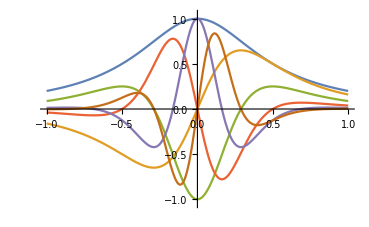

```mathematica
(* Each coefficient 'F_n' as function of the ratio Δ/κ *)
F0[Δ_,κ_]:=1/(1+(4 Δ^2)/κ^2);
F1[Δ_,κ_]:=(4 Δ κ^3)/((4 Δ^2+κ^2)^2);
F2[Δ_,κ_]:=-(κ^4 (-12 Δ^2+κ^2))/((4 Δ^2+κ^2)^3);
F3[Δ_,κ_]:=-(8 (κ^5 (-4 Δ^3+Δ κ^2)))/((4 Δ^2+κ^2)^4);
F4[Δ_,κ_]:=(κ^6 (80 Δ^4-40 Δ^2 κ^2+κ^4))/((4 Δ^2+κ^2)^5);
F5[Δ_,κ_]:=(4 κ^7 (48 Δ^5-40 Δ^3 κ^2+3 Δ κ^4))/((4 Δ^2+κ^2)^6);
(* without loss of generality, we make κ=1, because all 'F_n' only depends on the ratio Δ/κ anyway *)
Plot[{F0[Δ,1], F1[Δ,1],F2[Δ,1],F3[Δ,1],F4[Δ,1],F5[Δ,1]},{Δ,-1,1}, PlotRange->{-1.05, 1.05}]
```

```mathematica
(* Here we are plotting the actual optical force of the system, regardless of the modulation depth, i.e., ϵ=0 *)
OpticalForce[Δ_,κ_,X_,f0_]:=f0*(F0[Δ,κ]+ F1[Δ,κ]*X+F2[Δ,κ]*X^2+F3[Δ,κ]*X^3+F4[Δ,κ]*X^4+F5[Δ,κ]*X^5)

(* We can see that in the next plot that the general profile of the optical force drastically changes as the amplitude X increases, and the topology starts to kinda 'oscillate' in function of the detuning Δ *)
Manipulate[Plot[{OpticalForce[Δ,1,X,1],F0[Δ,1], F1[Δ,1]*X,F2[Δ,1]*X^2,F3[Δ,1]*X^3,F4[Δ,1]*X^4,F5[Δ,1]*X^5},{Δ,-2,2},PlotStyle->{Black,RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.58, 0.41000000000000003, 0.73],RGBColor[0.61, 0.45, 0]},PlotRange->{-3,3}],{X,0.5,1.5}]
```